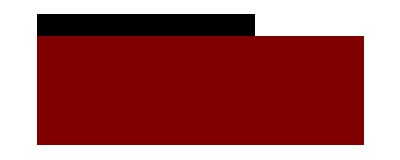

```mathematica
ArrayPlot[CellularAutomaton[{{3,0}->{3,2},{2,0}->{2,0},{1,0}->{1,0},{0,0}->{0,0},{3,1}->{3,3},{2,1}->{2,1},{1,1}->{1,1},{0,1}->{0,1},{3,2}->{3,2},{2,2}->{3,2},{1,2}->{1,2},{0,2}->{0,2},{3,3}->{3,3},{2,3}->{3,3},{1,3}->{1,3},{0,3}->{0,3}},{{3,3,3,3,3,3,3,3,3,3},0},5]]
```

```mathematica
{{1,1}->{0,1},{1,0}->{1,0},{0,1}->{0},{0,0}->{0,1}}
```

{{1,1}→{0,1},{1,0}→{1,0},{0,1}→{0},{0,0}→{0,1}}

```mathematica
{3,3}->{3,3},{2,3}->{3,3},{1,3}->{1,3},{0,3}->{0,3}
```

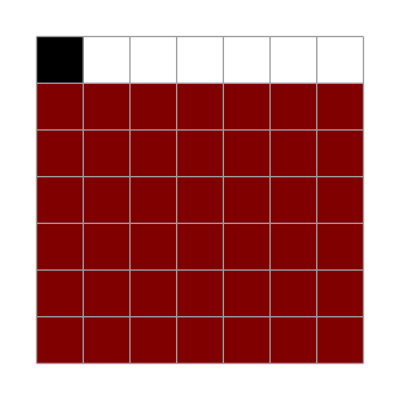

```mathematica
ArrayPlot[CellularAutomaton[{{3,0}->{3,2},{2,0}->{2,0},{1,0}->{1,0},{0,0}->{0,0},{3,1}->{3,3},{2,1}->{2,1},{1,1}->{1,1},{0,1}->{0,1},{3,2}->{3,2},{2,2}->{3,2},{1,2}->{1,2},{0,2}->{0,2},{3,3}->{3,3},{2,3}->{3,3},{1,3}->{1,3},{0,3}->{0,3}},{{1},0},6],Mesh-> True]
```

```mathematica
RulePlot[%242]
```

RulePlot[-Graphics-]

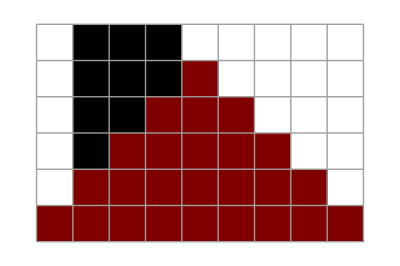

```mathematica
ArrayPlot[CellularAutomaton[{{0,1,1}->1,{0,0,1}->0,{1,1,0}->1,{0,0,0}->0,{1,1,1}->1},{{1,1,1},0},5],Mesh-> True]
```

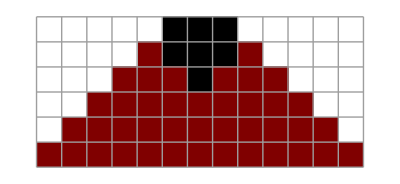

```mathematica
ArrayPlot[CellularAutomaton[{{0,1,1}->1,{1,1,0}->1,{0,0,0}->0,{1,1,1}->1},{{1,1,1},0},5],Mesh-> True]
```

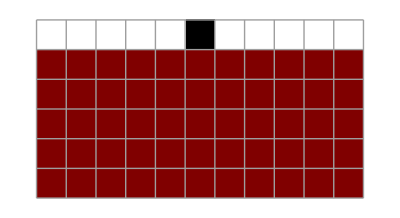

```mathematica
ArrayPlot[CellularAutomaton[{{0,1,1}->{0,1,1},{0,0,1}->{0,0,1},{0,1,0}->{0,1,0},{1,0,1}->{1,0,1},{1,0,0}->{1,0,0},{1,1,0}->{1,1,0},{0,0,0}->{0,0,0},{1,1,1}->{1,0,1}},{{1},0},5],Mesh-> True]
```

```mathematica
ArrayPlot[CellularAutomaton[{{0,_,1}->{0,_,1},{0,1,0}->{0,1,0},{1,0,0}->{1,_,0},{0,0,0}->{0,_,0}},{{1},0},5],Mesh-> True]
```

-Graphics-

```mathematica
RulePlot[CellularAutomaton[{{0,1}->1,{0,0}->0,{1,0}->1,{1,1}->0}]]
```

RulePlot[CellularAutomaton[{{0,1}→1,{0,0}→0,{1,0}→1,{1,1}→0}]]

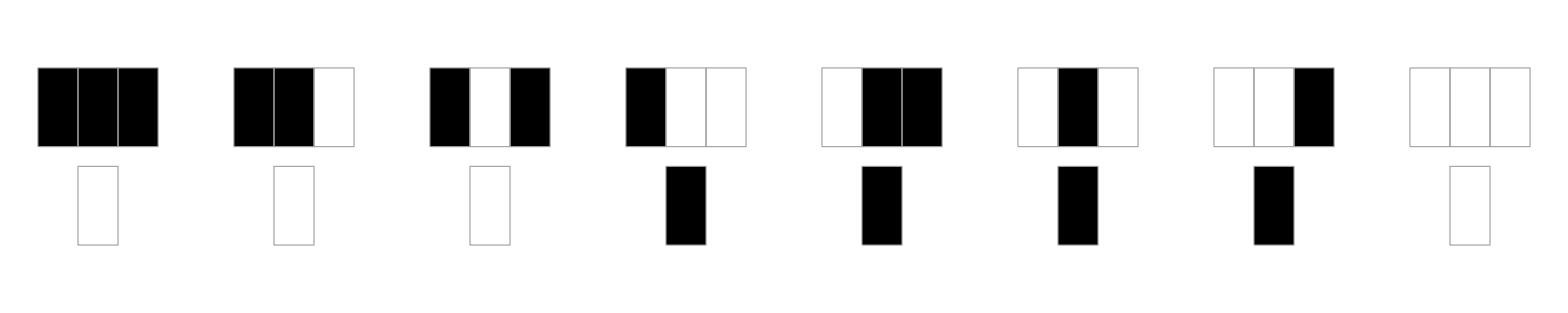

```mathematica
RulePlot[CellularAutomaton[30]]
```

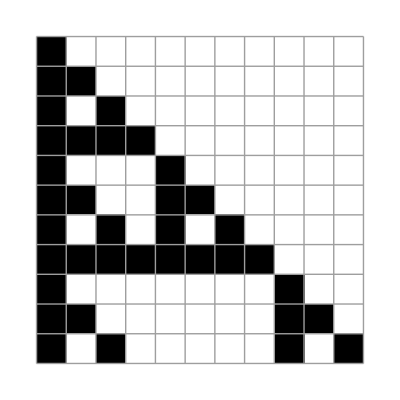

```mathematica
ArrayPlot[CellularAutomaton[{{0,1}->1,{0,0}->0,{1,0}->1,{1,1}->0},{{1},0},10],Mesh-> True]
```

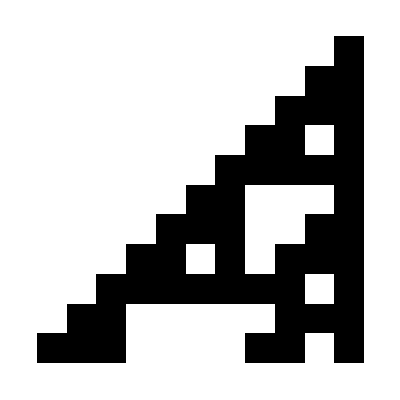
```mathematica
-Graphics-
RulePlot[%58]
```

-Graphics-

RulePlot[-Graphics-]

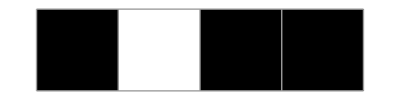

```mathematica
ArrayPlot[{{1,0,1,1}},Mesh-> True]
```

```mathematica
ArrayPlot[CellularAutomaton[{{3,0}->{3,2},{2,0}->{2,0},{1,0}->{1,0},{0,0}->{0,0},{3,1}->{3,3},{2,1}->{2,1},{1,1}->{1,1},{0,1}->{0,1},{3,2}->{3,2},{2,2}->{3,2},{1,2}->{1,2},{0,2}->{0,2},{3,3}->{3,3},{2,3}->{3,3},{1,3}->{1,3},{0,3}->{0,3}},{{1},0},6],Mesh-> True]
```

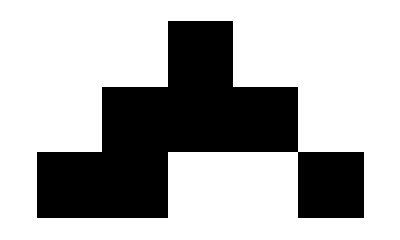

```mathematica
CellularAutomaton[{{p_,q_,r_}->Xor[p,Or[q,r]]},{{True},False},2]//Boole//ArrayPlot
```

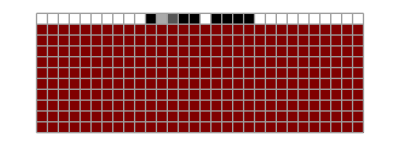

```mathematica
ArrayPlot[CellularAutomaton[{{3,0,3}-> {3,2,3},{2,0,3}-> {2,0,3},{1,0,3}-> {1,0,3},{0,0,3}-> {0,0,3},{3,0,2}-> {3,0,2},{2,0,2}-> {2,0,2},{1,0,2}-> {1,0,2},{0,0,2}-> {0,0,2},{3,0,1}-> {3,0,1},{2,0,1}-> {2,0,1},{1,0,1}-> {1,0,1},{0,0,1}-> {0,0,1},{3,0,0}-> {3,0,0},{2,0,0}-> {2,0,0},{1,0,0}-> {1,0,0},{0,0,0}-> {0,0,0},{3,1,3}-> {3,3,3},{2,1,3}-> {2,3,3},{1,1,3}-> {1,3,3},{0,1,3}-> {0,3,3},{3,1,2}-> {3,3,2},{2,1,2}-> {3,3,2},{1,1,2}-> {1,3,2},{0,1,2}-> {0,3,2},{3,1,1}-> {3,3,1},{2,1,1}-> {2,1,1},{1,1,1}-> {1,1,1},{0,1,1}-> {0,1,1},{3,1,0}-> {3,3,0},{2,1,0}-> {2,1,0},{1,1,0}-> {1,1,0},{0,1,0}-> {0,1,0},{3,2,3}-> {3,3,3},{2,2,3}-> {2,3,3},{1,2,3}-> {1,3,3},{0,2,3}-> {0,3,3},{3,2,2}-> {3,3,2},{2,2,2}-> {2,3,2},{1,2,2}-> {1,3,2},{0,2,2}-> {0,3,2},{3,2,1}-> {3,2,1},{2,2,1}-> {2,2,1},{1,2,1}-> {1,2,1},{0,2,1}-> {0,2,1},{3,2,0}-> {3,2,0},{2,2,0}-> {2,2,0},{1,2,0}-> {1,2,0},{0,2,0}-> {0,2,0},{3,3,3}-> {3,3,3},{2,3,3}-> {2,3,3},{1,3,3}-> {1,3,3},{0,3,3}-> {0,3,3},{3,3,2}-> {3,3,2},{2,3,2}-> {2,3,2},{1,3,2}-> {1,3,2},{0,3,2}-> {0,3,2},{3,3,1}-> {3,3,1},{2,3,1}-> {2,3,1},{1,3,1}-> {1,3,1},{0,3,1}-> {0,3,1},{3,3,0}-> {3,3,0},{2,3,0}-> {2,3,0},{1,3,0}-> {1,3,0},{0,3,0}-> {0,3,0}},{{3,1,2,3,3,0,3,3,3,3},0},10],Mesh-> True]
```

```mathematica
ArrayPlot[CellularAutomaton[{{3,0,3}-> {3,2,3},{2,0,3}-> {2,0,3},{1,0,3}-> {1,0,3},{0,0,3}-> {0,0,3},{3,0,2}-> {3,0,2},{2,0,2}-> {2,0,2},{1,0,2}-> {1,0,2},{0,0,2}-> {0,0,2},{3,0,1}-> {3,0,1},{2,0,1}-> {2,0,1},{1,0,1}-> {1,0,1},{0,0,1}-> {0,0,1},{3,0,0}-> {3,0,0},{2,0,0}-> {2,0,0},{1,0,0}-> {1,0,0},{0,0,0}-> {0,0,0},{3,1,3}-> {3,3,3},{2,1,3}-> {2,3,3},{1,1,3}-> {1,3,3},{0,1,3}-> {0,3,3},{3,1,2}-> {3,3,2},{2,1,2}-> {3,3,2},{1,1,2}-> {1,3,2},{0,1,2}-> {0,3,2},{3,1,1}-> {3,3,1},{2,1,1}-> {2,1,1},{1,1,1}-> {1,1,1},{0,1,1}-> {0,1,1},{3,1,0}-> {3,3,0},{2,1,0}-> {2,1,0},{1,1,0}-> {1,1,0},{0,1,0}-> {0,1,0},{3,2,3}-> {3,3,3},{2,2,3}-> {2,3,3},{1,2,3}-> {1,3,3},{0,2,3}-> {0,3,3},{3,2,2}-> {3,3,2},{2,2,2}-> {2,3,2},{1,2,2}-> {1,3,2},{0,2,2}-> {0,3,2},{3,2,1}-> {3,2,1},{2,2,1}-> {2,2,1},{1,2,1}-> {1,2,1},{0,2,1}-> {0,2,1},{3,2,0}-> {3,2,0},{2,2,0}-> {2,2,0},{1,2,0}-> {1,2,0},{0,2,0}-> {0,2,0},{3,3,3}-> {3,3,3},{2,3,3}-> {2,3,3},{1,3,3}-> {1,3,3},{0,3,3}-> {0,3,3},{3,3,2}-> {3,3,2},{2,3,2}-> {2,3,2},{1,3,2}-> {1,3,2},{0,3,2}-> {0,3,2},{3,3,1}-> {3,3,1},{2,3,1}-> {2,3,1},{1,3,1}-> {1,3,1},{0,3,1}-> {0,3,1},{3,3,0}-> {3,3,0},{2,3,0}-> {2,3,0},{1,3,0}-> {1,3,0},{0,3,0}-> {0,3,0}},{{3,1,2,3,3,0,3,3,3,3},0},5]]
```

```mathematica
unitOld[code_Integer]:=Module[{x,y},x:=If[code<2,Black,White];y:=If[EvenQ[code],Black,White] ;Framed[Graphics[{EdgeForm[{Thin,Black}],FaceForm[x],Rotate[Rectangle[{0,0}],Pi/4],EdgeForm[{Thin,Black}],FaceForm[y],Disk[{√2+√2/2,0.5},√2/2]},Frame->All,ImageSize->Tiny]]](* Rule Unit. Parameter code: 0 means data and parity missing, 1 means parity missing, 2 means data missing, 3 means data and parity available*)
```

```mathematica
unit[code_Integer]:= Module[{x,y},

x := If[ code<2, Black, White];

y := If[ EvenQ[code], Black, White];

Graphics[{

EdgeForm[{Thin,Black}],

FaceForm[x],

Rotate[Rectangle[{0,0}], Pi/4],

EdgeForm[{Thin,Black}],

FaceForm[y],

Disk[{√2+√2/2,0.5},√2/2]},

ImageSize->Tiny]](* Rule Unit. Parameter code: 0 means all missing, 1 means parity missing, 2 means data missing, 3 means all available*)
```

```mathematica
Grid[{{unit[0]},{unit[1]},{unit[2]},{unit[3]}}]
```

-Graphics-

```mathematica
Grid[Table[{unit[0],unit[1],unit[2],unit[3]},1],Frame->All]
```

-Graphics-

```mathematica
rule:={{0,0}-> {0,0},{1,0}-> {1,0},{2,0}-> {2,0},{3,0}-> {3,0},{0,1}-> {0,1},{1,1}-> {1,1},{2,1}-> {2,1},{3,1}-> {3,3},{0,2}-> {0,2},{1,2}-> {3,2},{2,2}-> {3,2},{3,2}-> {3,2},{0,3}-> {0,3},{1,3}-> {3,3},{2,3}-> {3,3},{3,3}-> {3,3}}
```

```mathematica
{unit[],unit[]}-> {unit[],unit[]}
```

```mathematica
takeLargestValue[x_, y_,z_]:= Module[{m,n, rules = rule},

m={x,y} /. rules;

n= {y,z}/.rules;

If[m[[2]]≥ n[[1]],m[[2]],n[[1]]]
]
```

```mathematica
chain = RandomInteger[3,10]
```

{3,2,2,2,0,2,3,3,3,1}

```mathematica
chain
```

{3,2,2,2,0,2,3,3,3,1}

```mathematica
Table[takeLargestValue[chain[[i]],chain[[i+1]],chain[[i+2]]],{i,Length[chain]-2}]
```

{3,3,2,0,3,3,3,3}

```mathematica
ClearAll[evalRules];

evalRules[row_List ]:=Join[

{({row[[1]],row[[2]]}/.rule)[[1]]},

Table[takeLargestValue[row[[i]],row[[i+1]],row[[i+2]]],{i,Length[row]-2}],

{({row[[-2]],row[[-1]]}/.rule)[[2]]}
]
```

```mathematica
evalRules[chain]
```

{3,3,3,2,0,3,3,3,3,3}

```mathematica
Grid[{Map[unit,evalRules[chain]]},Frame->All]
```

-Graphics-

```mathematica
Grid[{Map[unit,chain]},Frame-> All]
```

-Graphics-

```mathematica
Grid[Map[unit,FixedPointList[evalRules,chain],{2}],Frame-> All]
```

-Graphics-

```mathematica
aE[alpha_,horizontalS_,helicalS_]:= Module[{strands},
strands= horizontalS + (alpha-1)  helicalS;

]
```